```mathematica
(*■*)
```

## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"
jsonInfo[json]
```

Available:{plot2Doption,framelabel[xlabel_String,ylabel_String,size_:20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json

no. | title | length
1 | cpu_time | 606
2 | eq_of_motion | 606
3 | gauge0_intersection | 606
4 | gauge10_intersection | 606
5 | gauge11_intersection | 606
6 | gauge12_intersection | 606
7 | gauge13_intersection | 606
8 | gauge14_intersection | 606
9 | gauge15_intersection | 606
10 | gauge16_intersection | 606
11 | gauge17_intersection | 606
12 | gauge18_intersection | 606
13 | gauge19_intersection | 606
14 | gauge1_intersection | 606
15 | gauge20_intersection | 606
16 | gauge21_intersection | 606
17 | gauge22_intersection | 606
18 | gauge23_intersection | 606
19 | gauge2_intersection | 606
20 | gauge3_intersection | 606
21 | gauge4_intersection | 606
22 | gauge5_intersection | 606
23 | gauge6_intersection | 606
24 | gauge7_intersection | 606
25 | gauge8_intersection | 606
26 | gauge9_intersection | 606
27 | simulation_time | 606
28 | wall_clock_time | 606
29 | water_E | 606
30 | water_EK | 606
31 | water_EP | 606
32 | water_face_size | 606
33 | water_point_size | 606
34 | water_volume | 606

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,1]-importData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,2]-importData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,3]-importData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
Tshift=-7.55

ExpHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

-7.55

```mathematica
ζa=0.05/2;
{B,L}={0.74,0.997};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=5.;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]];

k=2π/L;
ω=Omega[k,h];
```

180.756

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

## 計算結果

```mathematica
fourColorScheme={
{Thick,Opacity[0.8],Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Opacity[0.8],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
(*PlotStyle->{{Blue},{Red},{Darker[Green]}},*)
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
```

```mathematica
simutime=importData[json,"simulation_time"]/Tw;
```

```mathematica
(*プロット*)
Column@Table[
ListLogPlot[Transpose[{Range[Length[#]],#}]&@@@importData[json,"eq_of_motion"][[;;100]],
PlotLabel->json,
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,1}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
],{json,
{json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json",
"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"}}]
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::take: eq_of_motion/.$Failedの1から100の位置が取れません．

Transpose::nmtx: {{},eq_of_motion}の最初の2個のレベルは転置できません．

Transpose::nmtx: {{},1}の最初の2個のレベルは転置できません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

ListLogPlot::lpn: Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListLogPlot::lpnのこれ以上の出力は表示されません．

Import::nffil: Importの最中にファイル/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::take: eq_of_motion/.$Failedの1から100の位置が取れません．

Transpose::nmtx: {{},eq_of_motion}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

ListLogPlot[Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧,PlotLabel→/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json,PlotRange→Automatic,PlotStyle→Directive[Thickness[Tiny],GrayLevel[0],Opacity[0.2]],FrameTicks→{{All,Automatic},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},None}},AspectRatio→1/2,FrameLabel→{Number of evaluations,error |Q|},Frame→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]
ListLogPlot[Transpose[{{},eq_of_motion}]⟦Transpose[{{},1}]⟧,PlotLabel→/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json,PlotRange→Automatic,PlotStyle→Directive[Thickness[Tiny],GrayLevel[0],Opacity[0.2]],FrameTicks→{{All,Automatic},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},None}},AspectRatio→1/2,FrameLabel→{Number of evaluations,error |Q|},Frame→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

この計算条件では，準ニュートン法の繰り返し計算7回で | Q | < 10^-12 にまで収束した．
浮体を増やすと，収束の速さは遅くなるものの収束する．

```mathematica
opt=Append[opt,{PlotStyle->plotstyle,
PlotRange->{All,Automatic},
PlotLegends->{"Present","Tanizawa 1997","Experiment"}}];
```

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,3⟧の部分5は存在しません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-(float_force/.$Failed)⟦1;;All,3⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,3⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-1. (float_force/.$Failed)⟦1;;All,3⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,3⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

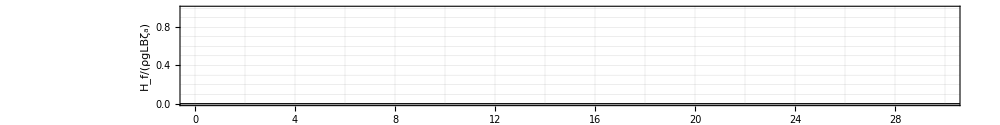

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,1⟧の部分5は存在しません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-(float_force/.$Failed)⟦1;;All,1⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,1⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,(-1. (float_force/.$Failed)⟦1;;All,1⟧⟦5⟧+(float_force/.$Failed)⟦1;;All,1⟧)/(B g L ζa ρ)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

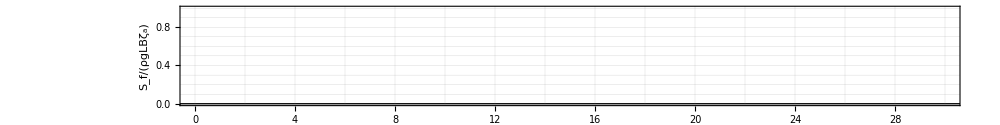

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_torque/.$Failed)⟦1;;All,2⟧の部分15は存在しません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(-(float_torque/.$Failed)⟦1;;All,2⟧⟦15⟧+(float_torque/.$Failed)⟦1;;All,2⟧)/(B^2 g L ζa ρ)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(1. (-1. (float_torque/.$Failed)⟦1;;All,2⟧⟦15⟧+(float_torque/.$Failed)⟦1;;All,2⟧))/(B^2 g L ζa ρ)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

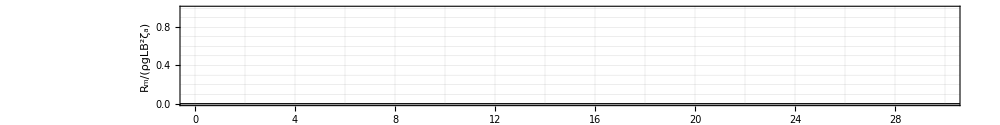

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,3⟧の部分5は存在しません．

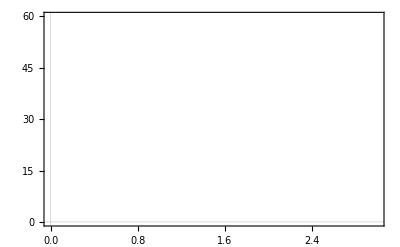

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_force/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_force/.$Failed)⟦1;;All,1⟧の部分5は存在しません．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_torque/.$Failed)⟦1;;All,2⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_torque/.$Failed)⟦1;;All,2⟧の部分15は存在しません．

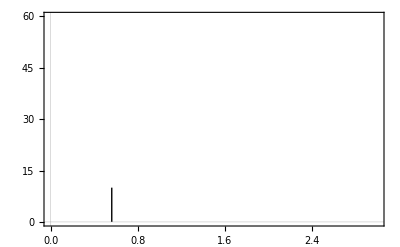

```mathematica
ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,3,3,1}],
SimuHf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,1,1,1}],
SimuSf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["S_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",i]-importData[json,"float_torque",i][[15]])/(ρ*g*L*B*B*ζa))}ᵀ,{i,2,2,1}],
SimuRm],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["R_m/(ρgLB^2ζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",3]-importData[json,"float_force",3][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuHf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",1]-importData[json,"float_force",1][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuSf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",2]-importData[json,"float_torque",2][[15]])/(ρ*g*L*B*B*ζa)),{15,30}],
interpolateAndFourierTr[SimuRm,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

浮体が流体から受ける，鉛直水平方向の力，y軸回転方向のトルクは，Tanizawa1997の結果とよく一致している．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,3⟧-(float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,3⟧-1. (float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

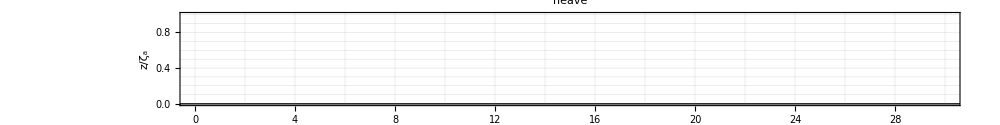

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,1⟧-(float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,((float_COM/.$Failed)⟦1;;All,1⟧-1. (float_COM/.$Failed))/ζa}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

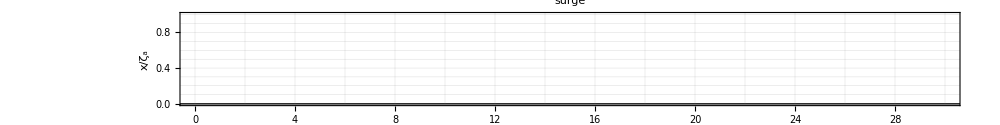

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(λ (float_pitch/.$Failed))/(2 π ζa)}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(0.1591549430918953 λ (float_pitch/.$Failed))/ζa}の最初の2個のレベルは転置できません．

Transpose::nmtx: {(simulation_time/.$Failed)/Tw,-(0.159155 λ (float_pitch/.$Failed))/ζa}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

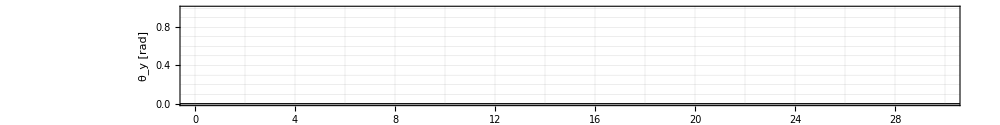

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

-Graphics-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

-Graphics-

```mathematica
ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa}ᵀ,
SimuHeave,
ExpHeave},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"heave",
Evaluate[plot2Doption]
]

ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa}ᵀ,
SimuSway,
ExpSway},
Evaluate[opt],
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"surge",
Evaluate[plot2Doption]
]

k=2π/λ;
ListPlot[
{{importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa)}ᵀ,
SimuRoll,
ExpRoll},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuHeave,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuSway,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa),{10,30}],
interpolateAndFourierTr[SimuRoll,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

ロール角を除き，浮体の並進移動は，Tanizawa1997の計算結果とよく一致している．一方の回転角度は，谷澤の結果よりも小さく

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)} cannot be transposed.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge0_intersection/.$Failed)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic,{-1.75 ζa,1.75 ζa}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge12_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge15_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge18_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-1. (gauge21_intersection/.$Failed)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic,{-1.75 ζa,1.75 ζa}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::partd: Part specification (gauge13_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {Automatic,{-1.75 ζa,1.75 ζa}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot::prng will be suppressed during this calculation.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

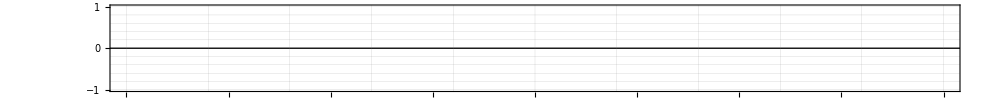
-Graphics-gauge0_intersection/.$Failed
-Graphics-gauge1_intersection/.$Failed
-Graphics-gauge2_intersection/.$Failed
-Graphics-gauge3_intersection/.$Failed
-Graphics-gauge4_intersection/.$Failed
-Graphics-gauge5_intersection/.$Failed
-Graphics-gauge6_intersection/.$Failed
-Graphics-gauge7_intersection/.$Failed
-Graphics-gauge8_intersection/.$Failed
-Graphics-gauge9_intersection/.$Failed
-Graphics-gauge10_intersection/.$Failed
-Graphics-gauge11_intersection/.$Failed
-Graphics-gauge12_intersection/.$Failed
-Graphics-gauge13_intersection/.$Failed
-Graphics-gauge14_intersection/.$Failed
-Graphics-gauge15_intersection/.$Failed
-Graphics-gauge16_intersection/.$Failed
-Graphics-gauge17_intersection/.$Failed
-Graphics-gauge18_intersection/.$Failed
-Graphics-gauge19_intersection/.$Failed
-Graphics-gauge20_intersection/.$Failed
-Graphics-gauge21_intersection/.$Failed
-Graphics-gauge22_intersection/.$Failed
-Graphics-gauge23_intersection/.$Failed

```mathematica
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

```mathematica
(*Mock-up for demonstration:Generates sample data similar to your structure*)
sampleData=ParallelTable[
Module[{data,DATA,position,w,v,fourier},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{w,v}=Transpose[interpolateAndFourierTr[{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,{10,15}]];
Transpose[{Table[i,{j,1,Length[w]}],w,v}]
],{i,1,20,1}];

minmax=MinMax[#3&@@@Flatten[sampleData,1]];

(*Visualization code*)
Graphics3D[Table[{ColorData["BlueGreenYellow"][sampleData[[i,j,3]]/minmax[[2]]],
Cuboid[{
sampleData[[i,j,1]],
sampleData[[i,j,2]],0},
{sampleData[[i,j,1]]+0.8,sampleData[[i,j,2]]+0.095,sampleData[[i,j,3]]}]},
{i,1,Length[sampleData]},{j,1,Length[sampleData[[i]]]}],Axes->True,BoxRatios->{1,1,1/2},PlotRange->{All,{0,3},All}]
```

-Graphics3D-

## 収束性のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json"
jsonInfo[json]
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
rbgs=Table["#"<>StringJoin[IntegerString[Round[#],16,2]&/@({255*Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i})],{i,0,1,0.2}]
hexColor="#"<>StringJoin[IntegerString[#,16,2]&/@rbgs[[1]]]


legend={(*"0.1",*)"0.09","0.08","0.07","0.06","0.05"}
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr}

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.jsonが見付かりませんでした．

no. | title | length

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{#000100,#4b0100,#7a0100,#7a0001,#4b0001,#010001}

##000100

{0.09,0.08,0.07,0.06,0.05}

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,3⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,3⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

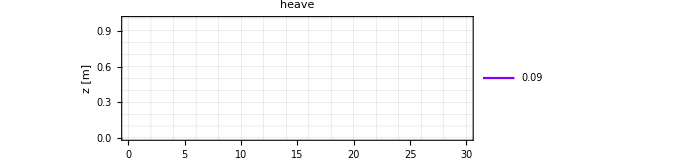

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,-(float_COM/.$Failed)⟦1;;All,1⟧⟦250⟧+(float_COM/.$Failed)⟦1;;All,1⟧}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

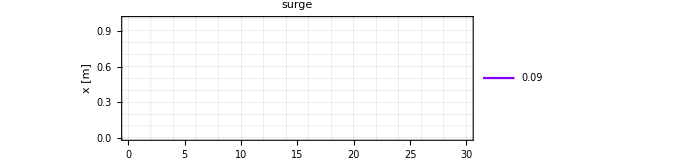

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(float_pitch/.$Failed)⟦250⟧-(float_pitch/.$Failed)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

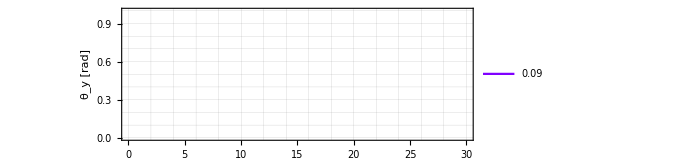

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d05/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt2={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",3]-importData[jsons[[i]],"float_COM",3][[250]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",1]-importData[jsons[[i]],"float_COM",1][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],-(importData[jsons[[i]],"float_pitch"]-importData[jsons[[i]],"float_pitch"][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

```mathematica
json1="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json"
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json1,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)} cannot be transposed.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)} cannot be transposed.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in …. An option must be a rule or a list of rules.

General::stop: Further output of ListPlot::nonopt will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)} cannot be transposed.

Transpose::nmtx: The first two levels of {simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Transpose::nmtx: {simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}の最初の2個のレベルは転置できません．

ListPlot::nonopt: …における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

General::stop: この計算中に，ListPlot::nonoptのこれ以上の出力は表示されません．

Part::partd: 部分指定(gauge1_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Transpose::nmtx: {simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

ListPlot[{Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge0_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge1_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge2_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge3_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge4_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge5_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge6_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge7_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge8_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge9_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge10_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge11_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge12_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge13_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge14_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge15_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge16_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge17_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge18_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge19_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge20_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge21_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge22_intersection/.$Failed
ListPlot[{Transpose[{simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)}],Transpose[{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}]},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge23_intersection/.$Failed

## 伝播の収束のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*start=18.15;
end=30;*)
start=0;
end=30;
```

Available:{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier,interpolateAndFourierTr,getOmegaFromKandDepth,getTFromLandDepth}

```mathematica
importData[filename_String,var_,n_: 0,replacement_: Missing[]]:=Module[{imported=Import[filename],processed},processed=imported/.{"NaN"|"Nan"|"null"|"nan"|Null->replacement};
If[n>0,(var/.processed)[[;;,n]],var/.processed]];

fileDir="/Volumes/home/BEM/benchmark202404";
(*fileDir="/Users/tomoaki/BEM";*)
```

```mathematica
jsons={
(*"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMlinear_ALElinear",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMlinear_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMpseudo_quad_ALElinear",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALElinear",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMpseudo_quad_ALElinear",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMlinear_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMpseudo_quad_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d03_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMpseudo_quad_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
*)
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad"};
jsons=FileNameJoin[{fileDir,#,"result.json"}]&/@jsons;
```

```mathematica
ExtractInfoFromPath[path_String]:=Module[{splitPath,mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod},splitPath=StringSplit[path,{"_","/"}];
(*Hの値を抽出*)
h=SelectFirst[splitPath,StringContainsQ[#,"H0d"]&];
h=StringReplace[h,{"H0d"->"H=0."}];

(*dtの値を抽出*)
dt=SelectFirst[splitPath,StringContainsQ[#,"DT0d"]&];
dt=StringReplace[dt,{"DT0d"->"dt=0."}];

(*meshの値を抽出*)
mesh=SelectFirst[splitPath,StringContainsQ[#,"float0d"]&];
mesh=StringReplace[mesh,{"float0d"->"dl=0."}];

(*BVPとIVPのための要素を抽出*)
elementBVPandIVP=SelectFirst[splitPath,StringContainsQ[#,"ELEM"]&];
elementBVPandIVP=StringReplace[elementBVPandIVP,"ELEM"->"BVP:"];

(*ALEの要素を抽出*)
elementALE=SelectFirst[splitPath,StringContainsQ[#,"ALE"]&];
elementALE=StringReplace[elementALE,"ALE"->"ALE:"];

(*ALE periodの値を抽出*)
ALEperiod=SelectFirst[splitPath,StringContainsQ[#,"ALEPERIOD"]&,"ALEPERIOD1"];
ALEperiod=StringReplace[ALEperiod,{"ALEPERIOD"->"ALE period:"}];


(*結果を返す*)
{mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod}];

(*gauges={"gauge2_intersection","gauge22_intersection"};*)
(*gauges={"gauge4_intersection","gauge23_intersection"};*)
gauges={"gauge2_intersection","gauge22_intersection"};
colors={Blue,Red,Darker[Green],Black};
(*---------------------------------------------*)
compare[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)



legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];
(*=======================================================================*)
Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.925,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,gauges}]]
,framelabel["Time [s]","water displacement [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
},
{
Labeled[
Row[Table[ListStepPlot[Table[{#1,#2}&@@@(interpolateAndFourier[#1,#2]&@@Transpose[selectAndNegateMean[json,name]]),{json,jsons}]
,Center
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio*2.
,ImageSize->size/2.
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.85,0.85}]]
,PlotRange->{{0.,3},{All,zrange[[2]]}(*,{0,0.026}*)}
,Joined->False
,Filling->Bottom
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]
],
{name,gauges}]]
,framelabel["Frequency [s^-1]","water displacement [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
]
]
(*=======================================================================*)
compareSimple[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)

legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];

Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio/1.5
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.05,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,{
"gauge2_intersection",
"gauge7_intersection",
"gauge12_intersection",
"gauge17_intersection",
"gauge22_intersection"}}]]
,framelabel["Time [s]","water displacement [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
,Spacings->0]
]
(*=======================================================================*)
fileName[{H_,L_,WAVE_,MESH_,DT_,ELEM_,ALE_}]:=Module[{formatNumber},
formatNumber[n_]:=StringReplace[ToString[N[n]],"."->"d"];
StringJoin["Tanizawa1996_",
"H",formatNumber[H],
"_L",formatNumber[L],
"_WAVE",WAVE,
"_MESH",MESH,
"_DT",formatNumber[DT],
"_ELEM",ELEM,
"_ALE",ALE]]
```

```mathematica
(*gaugeのx座標*)
FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[2]],1][[1]]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[1]],1][[1]]
```

/Volumes/home/BEM/benchmark202404/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.json

11.2

1.2

```mathematica
(*少しチェック*)
F=getOmegaFromLandDepth[1.8,50.]/(2*π)
T=1/F
```

0.93134

1.07372

```mathematica
2*π/getOmegaFromLandDepth[1.8,5.]
```

1.07372

#### 減衰へのALE毎回．meshの細かさの影響（おいおい）

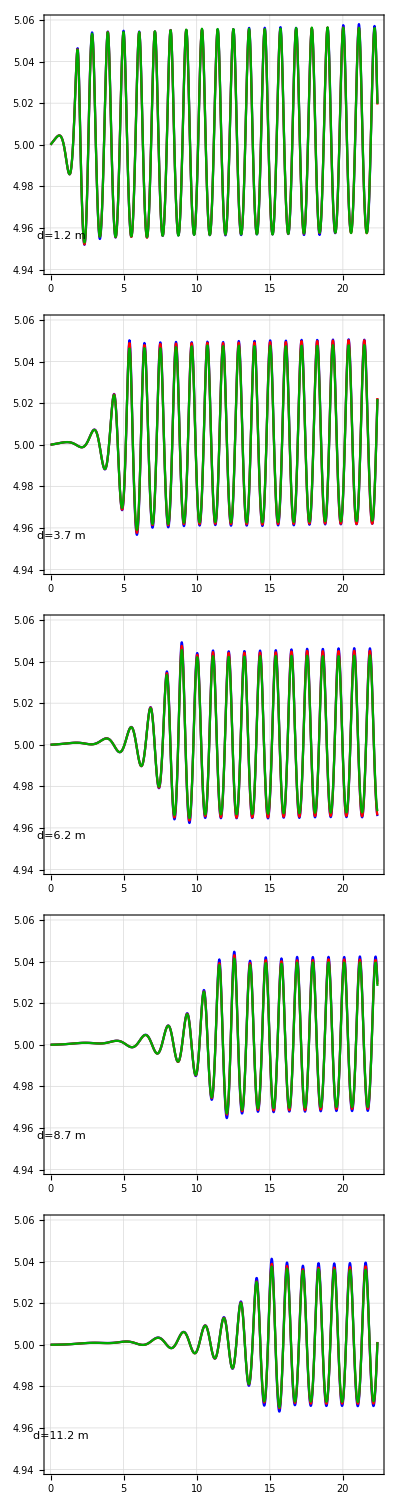
| 
-Graphics-Time [s]water displacement [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png

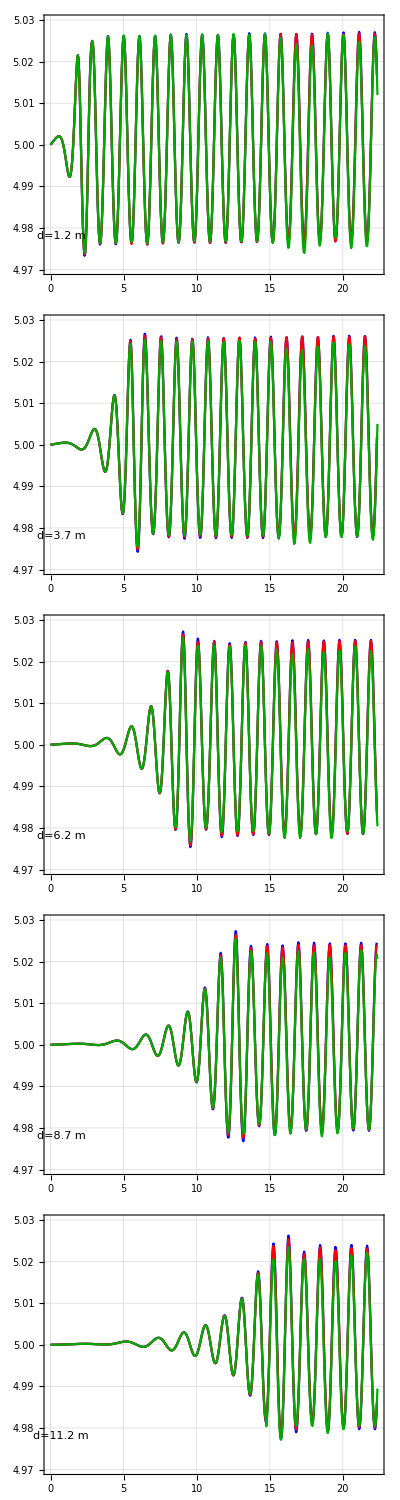
| 
-Graphics-Time [s]water displacement [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.06,0.06};
{start,end}={0.,17.+T*5};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};
fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png",fig,ImageResolution->200]

comp0d08={
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};

fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,{-0.03,0.03}]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png",fig,ImageResolution->200]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:linear

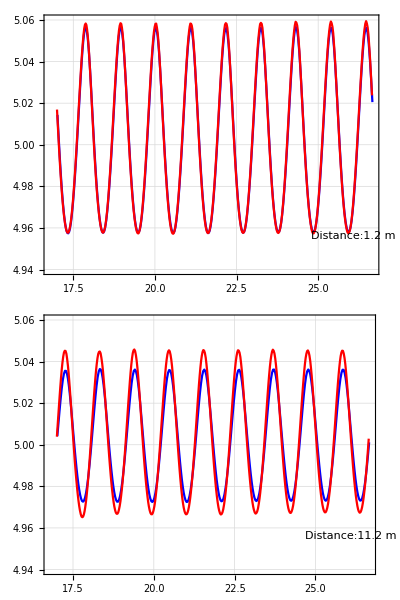
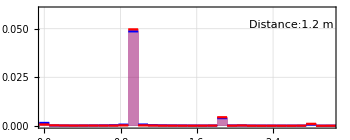
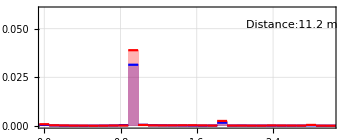
| 
-Graphics-Time [s]water displacement [m] | 
-Graphics--Graphics-Frequency [s^-1]water displacement [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={17.,17.+T*9};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};

fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png",fig,ImageResolution->200]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:pseudo-quad

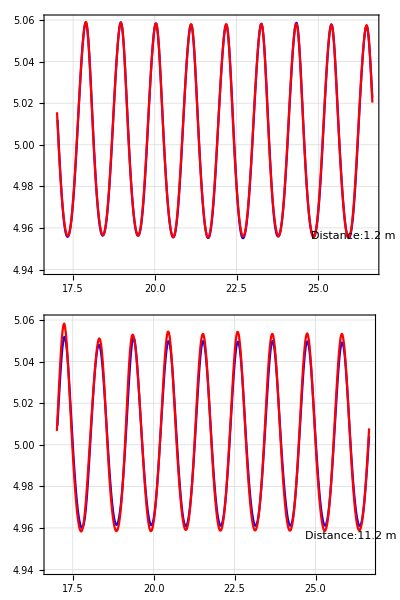
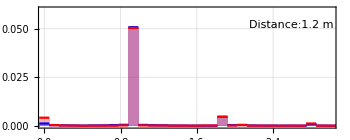
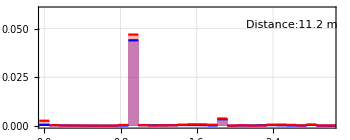
| 
-Graphics-Time [s]water displacement [m] | 
-Graphics--Graphics-Frequency [s^-1]water displacement [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={17.,17.+T*9};
ALE="pseudo_quad";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->200]

Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

#### BVPに擬2次要素を使った場合

{Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1,Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1}

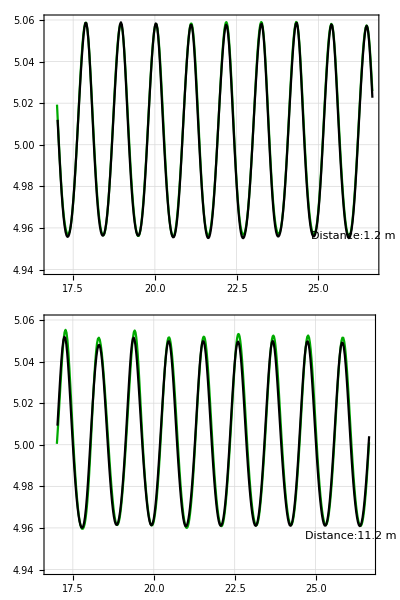
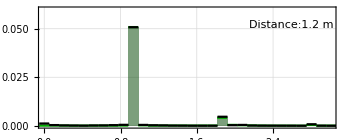
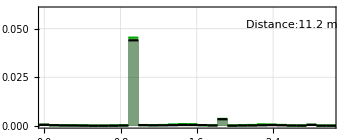
| 
-Graphics-Time [s]water displacement [m] | 
-Graphics--Graphics-Frequency [s^-1]water displacement [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png

ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．

```mathematica
zrange={-0.03,0.03}*2.;
colors=RotateLeft[colors,2];
ALE="pseudo_quad";
BVP="linear";
comp={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"}

compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png",%,ImageResolution->200]

Text["ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．"]
```

{141.12,152.64,190.08,204.48}

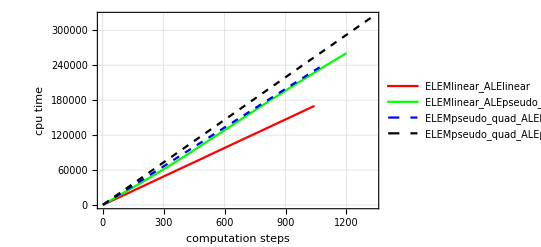

{141.12,152.64,190.08,204.48}

{1.,1.08163,1.34694,1.44898}

```mathematica
list={
"ELEMlinear_ALElinear",
"ELEMlinear_ALEpseudo_quad",
"ELEMpseudo_quad_ALElinear",
"ELEMpseudo_quad_ALEpseudo_quad"};
(*clist={5000,6000,7000,8000}*0.96;*)
clist={4900,5300,6600,7100}*0.96*0.03
Show[ListPlot[
Table[importData["/Volumes/home/BEM/benchmark202404/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_"<>name<>"/result.json","cpu_time"]
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","cpu time"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

clist
clist/clist[[1]]
```